# Mathematica: The Basics

## Rich Text Editor

Mathematica is a “rich text editor” similar to the .ipynb files of python and .mlx files of MATLAB, meaning that

plots and graphics will appear inline

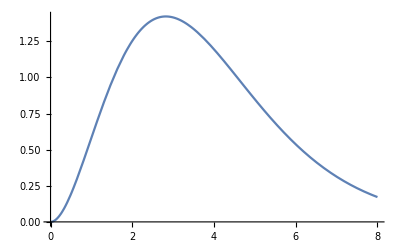

π^4/15

```mathematica
Plot[x^3/(Exp[x]-1),{x,0,8}]
Integrate[x^3/(Exp[x]-1),{x,0,∞}]
```

special characters can be inserted using the ctrl and esc button

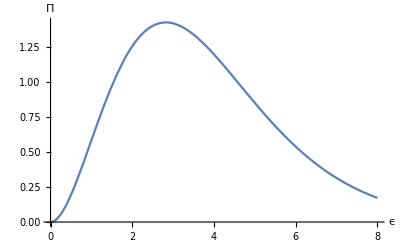

```mathematica
Plot[x^3/(Exp[x]-1),{x,0,8},AxesLabel->{"ϵ","Π"}]
∫x^3/(ⅇ^x-1)ⅆx
```

## A notebook is made from “cells”

Everything in Mathematica from text to input is contained within cells. See the brackets on the right side of this notebook? Those brackets demarcate cells

Press Shift+Enter to evaluate cell

Much of the formatting will apply to the entire cell

## Lists

Many functions in Mathematica return the output as lists. Accessing  lists requires syntax different than Python or MATLAB

```mathematica
list1 = {4,5,7,8}
list2 = Table[(n*(n-3))/2,{n,3,16}]
list3 = List[7,4,3,1]
list4 = {{1,2,3},{4,5,6},{7,8,9}}
```

{4,5,7,8}

{0,2,5,9,14,20,27,35,44,54,65,77,90,104}

{7,4,3,1}

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}
```

```mathematica
list2[[5]]
list4[[2]]
list4.list4
```

14

{4,5,6}

{{30,36,42},{66,81,96},{102,126,150}}

```mathematica
Length[list2]
Length[list4]
Length[list4[[2]]]
```

14

3

3

## Defining Functions makes Syntax even easier

### Define Function

Putting a ‘:’ before the equal sign esures that Mathematica updates the function every time it is called

```mathematica
a=2;
f[x_]:= (a*x^3)/(Exp[x]-1);
g[x_] = (a*x^3)/(Exp[x]-1);
```

```mathematica
f[2]-g[2]
a=4;
f[2]-g[2]
```

Your functions can contain as many variables as you want

## Manipulate - What a great feature

There are times when you’d like to explore a function and the dependence of different parameters on the output. 
Well, use Manipulate:

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,300,1}]
```

```mathematica
Manipulate[Plot[A*Sin[n*x]+B*Cos[n*x],{x,0,2 Pi}],{n,1,20},{A,1,5},{B,0,5}]
```